```mathematica
Integrate[Exp[-I n x],{x,0,Pi}]
```

-(ⅈ (1-ⅇ^(-ⅈ n π)))/n

```mathematica
Integrate[-Exp[-I n x],{x,-Pi,0}]
```

(ⅈ (-1+ⅇ^(ⅈ n π)))/n

```mathematica
Foo[n_]=1/(2Pi)(FullSimplify[Integrate[Exp[-I n x],{x,0,Pi}]+Integrate[-Exp[-I n x],{x,-Pi,0}]])
```

(ⅈ (-1+Cos[n π]))/(n π)

```mathematica
Foo[1]+Foo[-1]+Foo[2]+Foo[-2]
```

0

```mathematica
Foo[n_]=Simplify[Integrate[Exp[-I n x],{x,0,Pi}]+Integrate[-Exp[-I n x],{x,Pi,2Pi}]]
```

-(ⅈ ⅇ^(-2 ⅈ n π) (-1+ⅇ^(ⅈ n π))^2)/n

```mathematica
Simplify[Foo[Pi]+Foo[-Pi]+Foo[2Pi]+Foo[-2Pi]]
```

-(ⅈ ⅇ^(-4 ⅈ π^2) (1-4 ⅇ^(3 ⅈ π^2)+4 ⅇ^(5 ⅈ π^2)-ⅇ^(8 ⅈ π^2)))/(2 π)

```mathematica
Foo[1]
```

-4 ⅈ

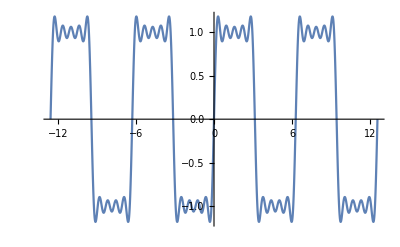

```mathematica
Plot[4/Pi(Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7+Sin[9x]/9),{x,-4Pi,4Pi}]
```

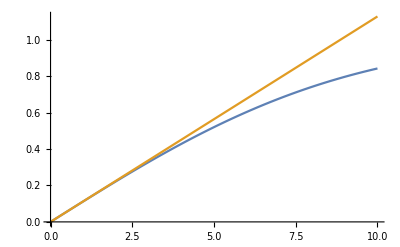

```mathematica
Plot[{Erf[x/10],1/(5 √π)x},{x,0,10}]
```

```mathematica
Integrate[Exp[I G r u],{u,-1,1}]
```

(2 Sin[G r])/(G r)

```mathematica
Simplify[Integrate[Sin[r]Erf[r]Exp[-r/L],{r,0,Infinity}]]
```

ConditionalExpression[(ⅇ^(-(ⅈ+L)^2/(4 L^2)) (ⅇ^(ⅈ/L) L (ⅈ+L) (1-ⅈ Erfi[(-ⅈ+L)/(2 L)])+(1+ⅈ L) L (-ⅈ+Erfi[(ⅈ+L)/(2 L)])))/(2 (1+L^2)),Re[L]>0]

```mathematica
Limit[(ⅇ^(-(ⅈ+L)^2/(4 L^2)) (ⅇ^(ⅈ/L) L (ⅈ+L) (1-ⅈ Erfi[(-ⅈ+L)/(2 L)])+(1+ⅈ L) L (-ⅈ+Erfi[(ⅈ+L)/(2 L)])))/(2 (1+L^2)),L->0]
```

0

```mathematica
Simplify[Assuming[g∈Reals&&r∈Reals&&a∈Reals&&L∈Reals,Integrate[ Exp[I*g* r
 Cos[the]](Erf[r/a]/r)Exp[-r/L]*(r*r*Sin[the]),{pi,0,2Pi},{the,0,Pi},{r,0,Infinity}]]]
```

(2 ⅇ^(-(a^2 (ⅈ+g L)^2)/(4 L^2)) π (ⅇ^((ⅈ a^2 g)/L) L (1-ⅈ g L) (ⅈ+Erfi[(a (-ⅈ+g L))/(2 L)])+L (1+ⅈ g L) (-ⅈ+Erfi[(a (ⅈ+g L))/(2 L)])))/(g+g^3 L^2)

```mathematica
Limit[(2 ⅇ^(-(a^2 (ⅈ+g L)^2)/(4 L^2)) π (ⅇ^((ⅈ a^2 g)/L) L (1-ⅈ g L) (ⅈ+Erfi[(a (-ⅈ+g L))/(2 L)])+L (1+ⅈ g L) (-ⅈ+Erfi[(a (ⅈ+g L))/(2 L)])))/(g+g^3 L^2),L->Infinity]
```

(4 ⅇ^(-1/4 a^2 g^2) π)/g^2